```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\2d_toolbox.wl"]
```

#### For a specific robot structure that consists only of triangles with no redundant modules and having one of 2 possible states for each module (long or short)

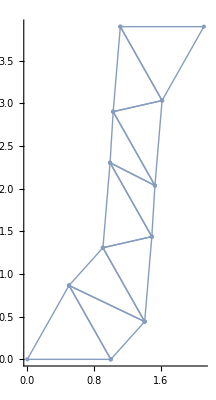

```mathematica
nrods =20;
shortlength = 0.6;
longlength = 1;
coords = MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]];
MeshAllTriag[coords,All]
```

#### If there are a large number of rods, collisions between rods tend to occur that can be detected

Did a collision occur?

True

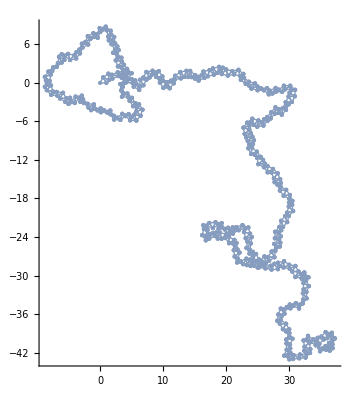

```mathematica
nrods =1000;
shortlength = 0.6;
longlength = 1;
coords = MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]];
Echo["Did a collision occur?"];
Echo[CollisionQ[coords,shortlength]];
MeshAllTriag[coords,All]
```

#### We can get an idea of the expected workspace of the mechanism (where the final point in the mechanism could go) by trying a series of random rod lengths

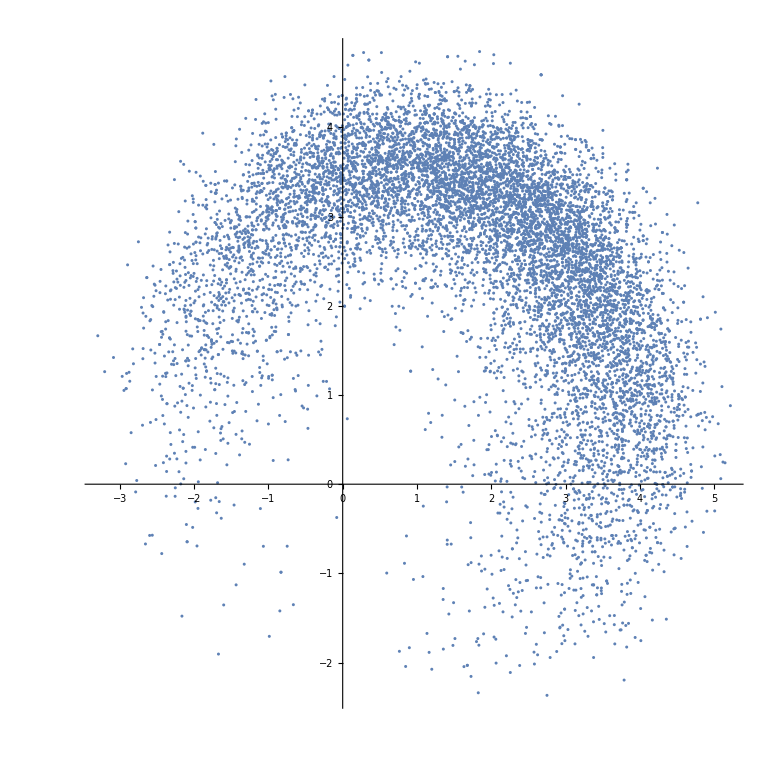

```mathematica
nrods =20;
shortlength = 0.6;
longlength = 1;
coords = Table[MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]],10000];
endeffector = coords[[All,-1,All]];
ListPlot[endeffector,PlotRange->All,AspectRatio->1]
```

#### Transitioning from a random state to its neighbour and then its neighbours’ neighbours.

```mathematica
nrods =50;
shortlength = 0.6;
longlength = 1;

fixed1 = {0,0};
fixed2 = {1,0};

Echo["a possible state {initial condition}"];
possiblestate =  MakeState[RandomInteger[2^nrods],nrods]

Echo["initial condition neighbours"];
ns =  FindNeighbours[possiblestate];(*//MatrixForm*)
ns //MatrixForm

Echo["First neighbours' neighbours"];
nns = FindNeighbours/@ns;
nns[[1]]//MatrixForm

g1 =Graph[Join[StateToNeighbours[possiblestate,Green],
Flatten[Table[StateToNeighbours[ns[[i]],Red],{i,Range[nrods]}]]]]
```

a possible state {initial condition}

{0.6,0.6,0.6,0.6,1,1,1,0.6,1,1,1,0.6,1,0.6,1,0.6,1,1,1,1,1,0.6,0.6,0.6,0.6,1,1,1,1,0.6,1,0.6,0.6,0.6,1,0.6,1,1,1,1,1,0.6,0.6,1,0.6,0.6,0.6,0.6,0.6,1}

initial condition neighbours

(1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1
0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6)

First neighbours' neighbours

(0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1
1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6)

-Graphics-

{1,0.6,1,1,1,0.6,0.6,0.6,1,0.6,0.6,0.6}

```mathematica
s =Rest@NestList[Flatten[Table[#->n,{n,FindNeighbours@#}]&/@#[[All,2]],1]&,{possiblestate->possiblestate},3];
Graph[Flatten[s]]
```

a possible state {initial condition}

{0.6,0.6,1,1,1,0.6,0.6,1,1,0.6,1,1}

initial condition neighbours

(1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6)

First neighbours' neighbours

(0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6)

-Graphics-

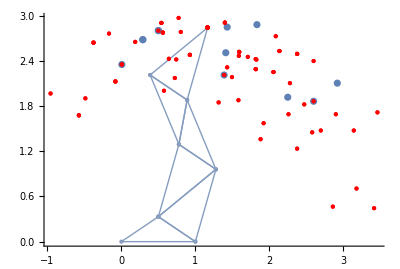

```mathematica
nc = MakeTriangleWorm[fixed1,fixed2,#]&/@ns;
nnc = MakeTriangleWorm[fixed1,fixed2,#]&/@Flatten[nns,1];
ne = nc[[All,-1,All]];
nne = nnc[[All,-1,All]];

g2 =Show[MeshAllTriag[MakeTriangleWorm[fixed1,fixed2,possiblestate],All],ListPlot[ne],ListPlot[nne,PlotStyle->{PointSize[Medium],Red}]]
```

#### Transition between all states

```mathematica
nrods=8;
shortlength=0.6;
longlength=1;
allstates=Tuples[{shortlength,longlength},nrods];
Graph[Flatten[StateToNeighbours[#,Black]&/@allstates]]
```

-Graphics-

#### Transition between many states

```mathematica
nrods =10;
shortlength = 0.6;
longlength = 1;
fixed1 = {0,0};
fixed2 = {1,0};

maxstates = 2^nrods;
chosenstates = MakeState[#,nrods]&/@RandomInteger[maxstates,1000];

FindNeighbours[state_]:=Table[FlipLength[state,i],{i,Length[state]}];
StateToNeighbours[state_,style_]:=state->#&/@FindNeighbours[state];
MakeState[statenumber_,nrods_]:=IntegerDigits[statenumber-1,2,nrods]/.{0->shortlength,0->longlength};
FlipLength[state_,index_]:=(
neighbour=state;
neighbour[[index]] =state[[index]]/.{0.6->1,1->0.6};
neighbour
)

transitions =Flatten[StateToNeighbours[#,Black]&/@chosenstates];
(*transitions = Tooltip[#,PlotCoordTransition[#]]&/@Flatten[StateToNeighbours[#,Black]&/@chosenstates];*)
```

```mathematica
g = Graph[RandomSample[transitions,400]]
```

-Graphics-

```mathematica
(*r = {1->2,1->3,1->4,4->6,8->12,12->8,13->8}*)
r=transitions;
gathfirst =GatherBy[r,First];
gathlast = GatherBy[r,Last];
firstsel = Select[gathfirst,Length[#]>nrods&];
lastsel = Select[gathlast,Length[#]>nrods&];
con = Join[firstsel,lastsel];

Graph[Flatten[con]]
```

{{{0.6,0.6,0.6,0.6}→{1,0.6,0.6,0.6},{0.6,0.6,0.6,0.6}→{0.6,1,0.6,0.6},{0.6,0.6,0.6,0.6}→{0.6,0.6,1,0.6},{0.6,0.6,0.6,0.6}→{0.6,0.6,0.6,1},{0.6,0.6,0.6,0.6}→{1,0.6,0.6,0.6},{0.6,0.6,0.6,0.6}→{0.6,1,0.6,0.6},{0.6,0.6,0.6,0.6}→{0.6,0.6,1,0.6},{0.6,0.6,0.6,0.6}→{0.6,0.6,0.6,1}},{{1,0.6,1,0.6}→{0.6,0.6,1,0.6},{1,0.6,1,0.6}→{1,1,1,0.6},{1,0.6,1,0.6}→{1,0.6,0.6,0.6},{1,0.6,1,0.6}→{1,0.6,1,1},{1,0.6,1,0.6}→{0.6,0.6,1,0.6},{1,0.6,1,0.6}→{1,1,1,0.6},{1,0.6,1,0.6}→{1,0.6,0.6,0.6},{1,0.6,1,0.6}→{1,0.6,1,1}},{{0.6,0.6,1,1}→{0.6,0.6,1,0.6},{0.6,1,1,0.6}→{0.6,0.6,1,0.6},{0.6,0.6,0.6,0.6}→{0.6,0.6,1,0.6},{0.6,0.6,0.6,0.6}→{0.6,0.6,1,0.6},{1,0.6,1,0.6}→{0.6,0.6,1,0.6},{1,0.6,1,0.6}→{0.6,0.6,1,0.6}}}

-Graphics-

```mathematica
r
```

```mathematica
$Aborted[]
```

```mathematica
First@transitions
```

{0.6,0.6,1,1}→{1,0.6,1,1}

```mathematica
Graph[transitions,VertexShapeFunction->(Inset[Framed@MeshAllTriag[MakeTriangleWorm[fixed1,fixed2,#2],{{0,1.5},{0,1.5}}],#1,Center,0.4]&),VertexSize-> .4]
```

-Graphics-

```mathematica
FindShortestTour
FindShortestPath[g,{0.6,0.6,1,1},{1,0.6,0.6,1},DistanceFunction->Sin[Norm[#,#2]]&]
```

FindShortestTour

FindShortestPath::nonopt: Options expected (instead of DistanceFunction→Sin[Norm[#1,#2]]&) beyond position 3 in …. An option must be a rule or a list of rules.

FindShortestPath[-Graphics-,{0.6,0.6,1,1},{1,0.6,0.6,1},DistanceFunction→Sin[Norm[#1,#2]]&]

```mathematica
FindPath
```